# One constraint max-entropy

```mathematica
findMaxEntropyDistribution[f_, F_,assumptions_,bounds_]:=Module[{g,Z,logZ,D1,soln,l,normalizationConstant},
	(*Define functions necessary for solving the system of equations.
	Assumptions: f is a function of one variable, and F a scalar.*)
	g[x_,a_]:=Exp[a f[x]];
	Z[a_]   :=Integrate[g[x,a],{x,bounds[[1]],bounds[[2]]},Assumptions->assumptions];
	logZ[a_]:=PowerExpand[Log[Z[a]],Assumptions->assumptions];
	D1[a_]  :=D[logZ[a],a];
	(* Solve system of equations. *)
	soln     =Solve[D1[a]==F, a,Assumptions->assumptions];
	(* Get argument of a that solves the equations. *)
	l        =a/.soln[[1,1]];
	normalizationConstant=Z[l];
	(* Resulting ME density is: *)
	g[x,l]/normalizationConstant
]

(* Ad hoc expansion of previous function so that Cauchy can also be solved. *)
findMaxEntropyDistribution2[f_,F_,assumptions_,bounds_]:=Module[{g,Z,logZ,D1,soln,l,normalizationConstant},
	g[x_,a_]:=Exp[a f[x]];
	Z[a_]   :=Integrate[g[x,a],{x,bounds[[1]],bounds[[2]]},Assumptions->assumptions];
	logZ[a_]:=PowerExpand[Log[Z[a]],Assumptions->assumptions];
	D1[a_]  :=D[logZ[a],a];
	soln     =Check[
					Solve[D1[a]==F, a,Assumptions->assumptions],
					FindInstance[D1[a]==F, a]
				];
	l        =a/.soln[[1,1]];
	normalizationConstant=Z[l];
	g[x,l]/normalizationConstant
]
```

### The Normal Distribution

```mathematica
bounds={-∞,∞};
f[x_]:=(x-μ)^2
F=σ^2;
assumptions=  σ>0 && μ∈Reals;
```

```mathematica
pNormal[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

Time it took to find this ME density: 0.875 s.

```mathematica
Manipulate[
	Plot[pNormal[x]/.{μ->m,σ->s},
		{x,-3,3},
		PlotRange->{0,0.5}
	],
	{{m,0,"μ"},-1,1, Appearance->"Labeled"},
	{{s,1,"σ"},0.5,2, Appearance->"Labeled"}
]
```

### Laplace

```mathematica
bounds={-∞,∞};
f[x_]:=Abs[x-μ];
F=b;
assumptions = a<0 && μ∈Reals && b>0;
```

```mathematica
pLaplace[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]
```

ⅇ^(-Abs[x-μ]/b)/(2 b)

Time it took to find this ME density: 1.18 s.

```mathematica
Manipulate[
	Plot[pLaplace[x]/.{μ->m,b->be},
		{x,-3,3},
		PlotRange->{0,0.5}
	],
	{{m,0,"μ"},-1,1, Appearance->"Labeled"},
	{{be,1,"b"},0.5,2, Appearance->"Labeled"}
]
```

### Exponential

```mathematica
bounds={0,∞};
f[x_]:=x
F=1/λ;
assumptions = a<0 && λ>0;
```

```mathematica
pExponential[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]
```

ⅇ^(-x λ) λ

Time it took to find this ME density: 0.05 s.

```mathematica
Manipulate[
	Plot[pExponential[x]/.{λ->l},
		{x,0,5},
		PlotRange->{0,1}
	],
	{{l,1,"λ"},0.5,2, Appearance->"Labeled"}
]
```

### Pareto

```mathematica
bounds={κ,∞}; 
f[x_]:=Log[x]
F=1/α+Log[κ];
assumptions =  κ>0 && α>0;
```

```mathematica
pPareto[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]
```

x^(-1-α) α κ^α

Time it took to find this ME density: 0.64 s.

```mathematica
Manipulate[
	Plot[pPareto[x]/.{κ->k,α->a},
		{x,k,5},
		PlotRange->{{0,5},{0,3}}
	],
	{{k,1,"κ"},0.5,3, Appearance->"Labeled"},
	{{a,1,"α"},0.5,3, Appearance->"Labeled"}
]
```

### Cauchy

With the Cauchy distribution, we run into trouble: the system of equations can’t be solved using normal methods.

```mathematica
bounds={-∞,∞}; 
f[x_]:=Log[1+x^2];
F=2 Log[2];
assumptions = a<0;
```

```mathematica
pCauchy[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

ReplaceAll::reps: {-PolyGamma[0,-1/2-a]+PolyGamma[0,-a]==2 Log[2]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Integrate::idiv: Integral of (1+x^2)^(a/.Log[4]+PolyGamma[0,-1/2-a]==PolyGamma[0,-a]) does not converge on {-∞,∞}.

(1+x^2)^(a/.-PolyGamma[0,-1/2-a]+PolyGamma[0,-a]==2 Log[2])/Integrate[(1+x^2)^(a/.-PolyGamma[0,-1/2-a]+PolyGamma[0,-a]==2 Log[2]),{x,-∞,∞},Assumptions→a<0]

So an ad-hoc approach is used: if a set of equations can’t be solved, find one instance of a solutions. In this case, it works. This is only possible since the Cauchy distribution has not parameters.

```mathematica
pCauchy[x_]=findMaxEntropyDistribution2[f,F,assumptions,bounds]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

FindInstance::ztest1: Unable to decide whether numeric quantity -EulerGamma-2 Log[2]-PolyGamma[0,1/2] is equal to zero. Assuming it is.

1/(π (1+x^2))

Time it took to find this ME density: 4.39 s.

### Test/unknown distribution

Now an experiment: try out some constraints for which I don’t know the correct ME-distribution.

#### Third moment

```mathematica
(* Known third moment on positive real domain *)
Clear[c]
bounds={0,∞};
f[x_]:=x^3;
F= c;
assumptions =  c>0;
pThirdPos[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]//Timing
pThirdPos[x_]=pThirdPos[x][[2]];
```

{1.84375,(3^(2/3) ⅇ^(-x^3/(3 c)))/(c^(1/3) Gamma[1/3])}

```mathematica
Manipulate[
	Plot[pThirdPos[x]/.{c->δ},
		{x,0,5},
		PlotRange->{{0,5},{0,3}}
	],
	{{δ,1,"k"},0.1,5, Appearance->"Labeled"}
]
```

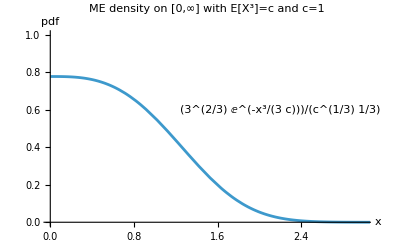

```mathematica
(* Create Figure for thesis*)
δ=1;
plot = Plot[pThirdPos[x]/.{c->δ},
		{x,0,5},
		PlotRange->{{0,3},{0,1}},
		AxesLabel->{x,"pdf"},
		PlotLabel->"ME density on [0,∞] with E[X^3]=c and c=1"
	];
eq = Text[pThirdPos[x], {2.2,0.6}];
txt = Graphics[{eq}];
Show[plot,txt]
```

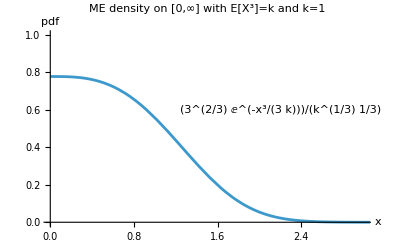

```mathematica
(* Known third moment on real domain *)
Clear[k]
bounds={-∞,∞};
f[x_]:=x^3;
F= k;
assumptions =  k>0;
pThirdReal[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]//Timing
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1,1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1.03125,(ⅇ^(x^3 (a/.{}⟦1,1⟧)))/Integrate[ⅇ^(x^3 (a/.{}⟦1,1⟧)),{x,-∞,∞},Assumptions→k>0]}

No solutions can be found, which is not surprising.

#### Second moment

```mathematica
(*Gaussian on half interval -> Exponential*)
bounds={0,∞}; 
f[x_]:=x^2;
F= k;
assumptions = a<0 && k>0;
findMaxEntropyDistribution[f,F,assumptions,bounds]//Timing
```

{0.078125,(ⅇ^(-x^2/(2 k)) √(2/π))/(√k)}

(Gives a special case of the normal distribution)

#### Square root

```mathematica
bounds={0,∞};
f[x_]:=Sqrt[x];
F= k;
assumptions = a<0 && k>0;
pSqrt[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]//Timing
pSqrt[x_]=pSqrt[x][[2]];
```

{1.5625,(2 ⅇ^(-(2 √x)/k))/k^2}

```mathematica
Manipulate[
	Plot[pSqrt[x]/.{k->δ},
		{x,0,5},
		PlotRange->{{0,5},{0,3}}
	],
	{{δ,1,"k"},0.5,7, Appearance->"Labeled"}
]
```

#### Truncated normal

```mathematica
bounds={a,b};
f[x_]:=(x-μ)^2
F=σ^2;
assumptions=  σ>0 && μ∈Reals &&  a<b && a∈Reals && b∈Reals;
pNew[x_]=findMaxEntropyDistribution[f,F,assumptions,bounds]//Timing
pNew[x_]=pNew[x][[2]];
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

ReplaceAll::reps: {-1/(2 a)+((2 ⅈ ⅇ^Times[«2»] (Power[«2»]+Times[«3»]))/(√π)+(ⅈ ⅇ^Times[«2»] (b+Times[«2»]))/(√Times[«2»] √π))/(ⅈ Erf[«1»]-ⅈ Erf[«1»])-ⅈ ((2 ⅈ ⅇ^Times[«2»] (Power[«2»]+Times[«3»]))/(√π)+(ⅈ ⅇ^Times[«2»] (b+Times[«2»]))/(√Times[«2»] √π)) (Piecewise[{{0, Greater[«2»]}, {Indeterminate, True}}]) Arg'[ⅈ Erf[«1»]-ⅈ Erf[«1»]]==σ^2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{4.90625,ⅇ^((x-μ)^2 (a/.-1/(2 a)+((2 ⅈ ⅇ^(a (a-μ)^2) (√-a-(a-μ)/(2 √-a)))/(√π)+(ⅈ ⅇ^(a (b-μ)^2) (b-μ))/(√-a √π))/(ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)])-ⅈ ((2 ⅈ ⅇ^(a (a-μ)^2) (√-a-(a-μ)/(2 √-a)))/(√π)+(ⅈ ⅇ^(a (b-μ)^2) (b-μ))/(√-a √π)) (Piecewise[{{0, 1/4-Arg[ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)]]/(2 π)>Floor[1/4-Arg[ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)]]/(2 π)]}, {Indeterminate, True}}]) Arg'[ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)]]==σ^2))/Integrate[ⅇ^((x-μ)^2 (a/.-1/(2 a)+((2 ⅈ ⅇ^(a (a-μ)^2) (√-a-(a-μ)/(2 √-a)))/(√π)+(ⅈ ⅇ^(a (b-μ)^2) (b-μ))/(√-a √π))/(ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)])-ⅈ ((2 ⅈ ⅇ^(a (a-μ)^2) (√-a-(a-μ)/(2 √-a)))/(√π)+(ⅈ ⅇ^(a (b-μ)^2) (b-μ))/(√-a √π)) (Piecewise[{{0, 1/4-Arg[ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)]]/(2 π)>Floor[1/4-Arg[ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)]]/(2 π)]}, {Indeterminate, True}}]) Arg'[ⅈ Erf[√-a (a-μ)]-ⅈ Erf[√-a (b-μ)]]==σ^2)),{x,a,b},Assumptions→σ>0&&μ∈ℝ&&a<b&&a∈ℝ&&b∈ℝ]}